## Installations

### Initializations

```mathematica
Clear["Global`*"]
Needs["SymbolicC`"];
targetDir=NotebookDirectory[];
SetDirectory[targetDir];
```

### Install Packages: Nbody.

```mathematica
MyPackageDirectory=ToFileName[{ParentDirectory[ParentDirectory[]],"Packages"}]
```

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/4-Artikulurako-I/C-inplementazioa/Packages/

```mathematica
Get["NBodyProblem`",Path->MyPackageDirectory];
Get["MyFunctions`",Path->MyPackageDirectory];
```

NBodyHam2::shdw: Symbol NBodyHam2 appears in multiple contexts {NBodyProblem`,Global`}; definitions in context NBodyProblem` may shadow or be shadowed by other definitions.

### Plot Style

```mathematica
StyleQuad=Red;
StyleIdeal=Black;
StyleMachine=Lighter[Blue,.6];
StyleClassic=Lighter[Gray,.6];
StyleError=Black;
StyleEstimation=Lighter[Blue,.6];
MarkerQuad="○"; (*○  △    □*)
MarkerIdeal="▲"; (*●  ▲  ■*)
MarkerMachine="■";
```

## Filenames

```mathematica
DataDirectory="Data/";
ImagesDirectory="Images/";
```

```mathematica
filey0=NotebookDirectory[]<>DataDirectory<>"Datay0.bin";
fileA=NotebookDirectory[]<>DataDirectory<>"outA.bin";
fileB=NotebookDirectory[]<>DataDirectory<>"outB.bin";
fileC=NotebookDirectory[]<>DataDirectory<>"outC.bin";
```

## Parameters (N9-Body Problem)

### Problem parameters and initial values DE430.

```mathematica
prec=100;
n=10;
neq=60;
```

```mathematica
q={0.00450250878464055477,0.00076707642709100705,0.00026605791776697764,
    0.36176271656028195477,-0.09078197215676599295,-0.08571497256275117236,
  0.61275194083507215477,-0.34836536903362219295,-0.19527828667594382236,
0.12051741410138465477,-0.92583847476914859295,-0.40154022645315222236,
-0.11018607714879824523,-1.32759945030298299295,-0.60588914048429142236,
-5.37970676855393644523,-0.83048132656339789295,-0.22482887442656542236,
7.89439068290953155477, 4.59647805517127300705 ,1.55869584283189997764,
-18.26540225387235944523,-1.16195541867586999295,-0.25010605772133802236,
-16.05503578023336944523,-23.94219155985470899295,-9.40015796880239402236,
-30.48331376718383944523,-0.87240555684104999295, 8.91157617249954997764};
```

```mathematica
v={-0.00000035174953607552,0.00000517762640983341, 0.00000222910217891203,
     0.00336749397200575848, 0.02489452055768343341, 0.01294630040970409203,
    0.01095206842352823448, 0.01561768426786768341, 0.00633110570297786403,
    0.01681126830978379448, 0.00174830923073434441, 0.00075820289738312913,
    0.01448165305704756448, 0.00024246307683646861,-0.00028152072792433877,
    0.00109201259423733748,-0.00651811661280738459,-0.00282078276229867897,
   -0.00321755651650091552, 0.00433581034174662541, 0.00192864631686015503,
   0.00022119039101561468,-0.00376247500810884459,-0.00165101502742994997,
   0.00264276984798005548,-0.00149831255054097759,-0.00067904196080291327,
   0.00032220737349778078,-0.00314357639364532859,-0.00107794975959731297};
```

```mathematica
u=Flatten[{q,v}];
```

```mathematica
Gm={0.295912208285591100*(10^-3),0.491248045036476000*(10^-10),0.724345233264412000*(10^-9),0.888769244512563400*(10^-9)+0.109318945074237400*(10^-10),0.954954869555077000*(10^-10),0.282534584083387000*(10^-6),0.845970607324503000*(10^-7),0.129202482578296000*(10^-7),
0.152435734788511000*(10^-7),0.217844105197418000*(10^-11)}; (*sun,Mercury,Venus,,Earth+Moon,Mars,Jupiter,Saturn,Uranus,Neptune,Pluto*)
```

```mathematica
preal=parameters=Gm;
pint={0,0};
```

```mathematica
u0=Chdata[u,preal];
u0D=N[u0];
u0DD=SetPrecision[u0D,prec];
ee0 =u0 - u0DD;
```

```mathematica
stru0=ExportString[u0,"Real128"];
stre0 = ExportString[u0*0.0,"Real128"];
strrpar = ExportString[preal, "Real128"];
```

```mathematica
N[ee0,20]
```

{-3.×10^-19,0.,0.,6.8×10^-18,0.,0.,-5.×10^-17,0.,0.,-3.×10^-18,0.,0.,-4.×10^-18,0.,0.,-2.75×10^-16,0.,0.,-3.1×10^-17,0.,0.,-3.71×10^-16,0.,0.,1.546×10^-15,0.,0.,9.155×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

### Integration parameters.

```mathematica
t0=0.;tend=1000000.;(*10000.*)
tend=1000.;
h=2.;
sampling=100;
sampling=1;
```

```mathematica
codfun0=2; (*NBody Problem*)
codfunX=12; (*NBody ProblemX*)
approx = 1; 
ns= 6;
nstep=(tend-t0)/h;
nout=nstep/sampling
```

500.

### RKG parameters

```mathematica
neq=60;
prec=100;
HAM=NBodyHam2;
```

## Analisis-I

### Import and mean

```mathematica
noutA=Round[nout]+1;
nstat=10; 
step=4;
dd1= (2neq+1);
dd2= (3neq+1);
```

```mathematica
outA=SetPrecision[ArrayReshape[BinaryReadList[fileA,"Real128"],{nstat,noutA,dd1}],prec];
outB=SetPrecision[ArrayReshape[BinaryReadList[fileB,"Real128"],{nstat,noutA,dd1}],prec];
outC=SetPrecision[ArrayReshape[BinaryReadList[fileC,"Real64"],{nstat,noutA,dd2}],prec];
tpA=Flatten[Take[outA[[1]],All,{1,1}]];
tpA=Map[First,Partition[tpA,step]];
tpB=Flatten[Take[outB[[1]],All,{1,1}]];
tpB=Map[First,Partition[tpB,step]];
tpC=Flatten[Take[outC[[1]],All,{1,1}]];
tpC=Map[First,Partition[tpC,step]];
```

```mathematica
{Length[outA],Length[outA[[1]]]}
```

{10,501}

```mathematica
{Length[outB],Length[outB[[1]]]}
```

{10,501}

```mathematica
{Length[outC],Length[outC[[1]]]}
```

{10,501}

```mathematica
{MeanHamA,DesvHamA,MeanErrA,EndHamA}=FunMeanHerr[outA,outA, nstat,noutA,HAM, parameters,neq,prec,step] ;
{MeanHamB,DesvHamB,MeanErrB,EndHamB}=FunMeanHerr[outB,outA, nstat,noutA,HAM, parameters,neq,prec,step] ;
{MeanHamC,DesvHamC,MeanErrC, EndHamC}=FunMeanHerr[outC,outA, nstat,noutA,HAM, parameters,neq,prec,step] ;
```

```mathematica
HamerrA=FunHerr[outA,nstat,noutA,HAM, parameters,neq,prec,step] ;
HamerrB=FunHerr[outB,nstat,noutA,HAM, parameters,neq,prec,step] ;
HamerrC=FunHerr[outC,nstat,noutA,HAM, parameters,neq,prec,step] ;
```

### Graphics-I (Energy)

```mathematica
MeanHamAdata = Transpose[{tpA,MeanHamA}];
MeanHamBdata = Transpose[{tpB,MeanHamB}];
MeanHamCdata = Transpose[{tpC,MeanHamC}];
DesvHamAdata = Transpose[{tpA,DesvHamA}];
DesvHamBdata = Transpose[{tpB,DesvHamB}];
DesvHamCdata = Transpose[{tpC,DesvHamC}];
```

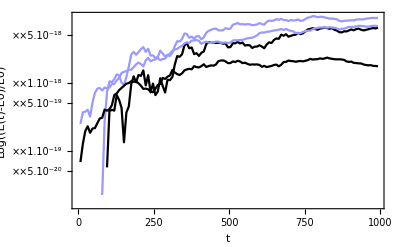

```mathematica
plot=ListLogPlot[{MeanHamBdata,MeanHamCdata,DesvHamBdata,DesvHamCdata},AxesLabel->{"t","Log((E(t)-E0)/E0)"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Log((E(t)-E0)/E0)"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot6a.pdf",Show[plot] ];
```

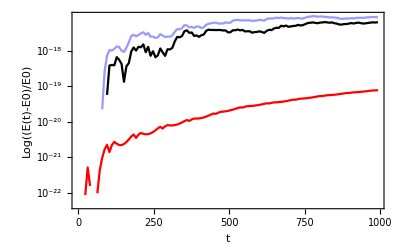

```mathematica
plot=ListLogPlot[{MeanHamAdata,MeanHamBdata,MeanHamCdata},AxesLabel->{"t","Log((E(t)-E0)/E0)"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleQuad,StyleIdeal,StyleMachine},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Log((E(t)-E0)/E0)"}]
```

### Graphics-II (Global Error)

```mathematica
MeanErrAdata = Transpose[{tpA,MeanErrA}];
MeanErrBdata = Transpose[{tpB,MeanErrB}];
MeanErrCdata = Transpose[{tpC,MeanErrC}];
```

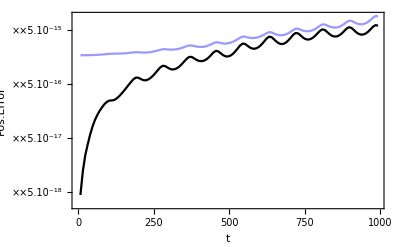

```mathematica
plot=ListLogPlot[{Drop[MeanErrBdata,1],Drop[MeanErrCdata,1]},AxesLabel->{"t","Pos.Error"},Joined->True,PlotRange->All,
(*PlotLegends->Placed[{"ideal","rdigits=0"(*,"rdigits=3"*)},Below],*)
(*PlotRange->All,*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot6b.pdf",Show[plot] ];
```

### Graphics-III (Histogram)

#### Ideal

0.00005204817237625435270648086788705946077274001645194241040481071392584263035237167

0.0003278233660279122732194289390362752502951505596181145595268353132991021176430134

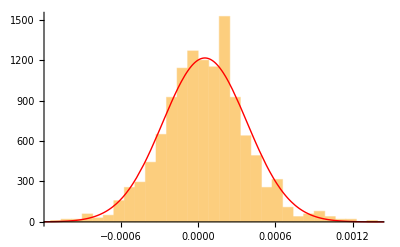

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/4-Artikulurako-I/C-inplementazioa/Experiments/Nbody  (solar-system)/Images/brouwer4e.pdf

```mathematica
Hamerdif=HamerrB 10^15;
μ=Mean[Hamerdif]
σ=StandardDeviation[Hamerdif]
ir1=Histogram[Hamerdif,{σ/4},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[NotebookDirectory[]<>ImagesDirectory<>"brouwer4e.pdf",Show[ir1,ir2]]
```

#### Machine precision (rdigits=0)

0.00007292312278693461255677842251901547818086597245142023366274856702347314480365881

0.00058416798486233240201428754016137835439842842067252355420250732243857038410690877

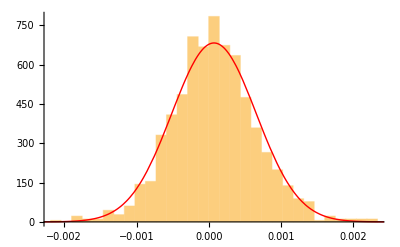

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/4-Artikulurako-I/C-inplementazioa/Experiments/Nbody  (solar-system)/Images/brouwer4f.pdf

```mathematica
Hamerdif=HamerrC 10^15;
μ=Mean[Hamerdif]
σ=StandardDeviation[Hamerdif]
ir1=Histogram[Hamerdif,{σ/4},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[NotebookDirectory[]<>ImagesDirectory<>"brouwer4f.pdf",Show[ir1,ir2]]
```

### Tables

#### Quadruple

```mathematica
MeanD0=0.; (*(SD0A/nstat)/steps*100;*)
MaxDE=Max[MeanHamA]//N;
Hamerdif=Drop[MeanHamA ,1]-Drop[ MeanHamA,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrA]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,7.81398×10^-20,6.30159×10^-22,5.94306×10^-22,0.}

#### Ideal

```mathematica
MeanD0=0.;(*(SD0B/nstat)/steps*100;*)
MaxDE=Max[MeanHamB]//N;
Hamerdif=Drop[MeanHamB ,1]-Drop[ MeanHamB,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrB]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,6.47981×10^-18,5.20482×10^-20,2.741×10^-19,6.14192×10^-15}

#### Machine

```mathematica
MeanD0=0.;(*(SD0C/nstat)/steps*100;*)
MaxDE=Max[MeanHamC]//N;
Hamerdif=Drop[MeanHamC ,1]-Drop[ MeanHamC,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrC]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,9.56323×10^-18,7.29231×10^-20,3.0403×10^-19,9.00695×10^-15}

## Analisis-II: error estimation

### Estimation

```mathematica
MeanErrCdata = Transpose[{tpC,MeanErrC}];
```

```mathematica
{MeanEstC,DesvEstC,MeanQtyC,DesvQtyC}=FunMeanEst[outC,outA,nstat,noutA,neq,prec,step];
```

```mathematica
MeanEstCdata = Transpose[{tpC,MeanEstC}];
DesvdataC1=Transpose[{tpC,MeanEstC+DesvEstC}];
DesvdataC2=Transpose[{tpC,MeanEstC-DesvEstC}];
```

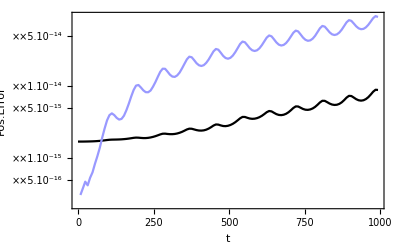

```mathematica
plot=ListLogPlot[{Abs[MeanErrCdata],Abs[MeanEstCdata]},AxesLabel->{"t","Pos.Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
PlotTheme->"Detailed",
PlotStyle->{StyleError,StyleEstimation},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot7a.pdf",Show[plot]];
```

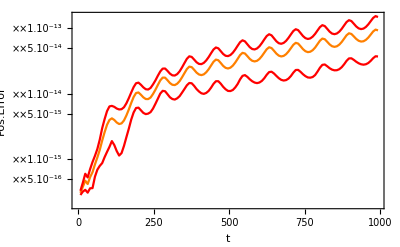

```mathematica
plot6b=ListLogPlot[{ MeanEstCdata,
                                          DesvdataC1,DesvdataC2},
AxesLabel->{"t","Pos.Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
PlotTheme->"Detailed",
PlotStyle->{Orange,Red,Red},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
```

### Quality estimation

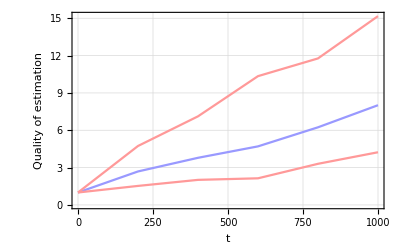

```mathematica
MeanQtyCdata=Transpose[{tpC,10^MeanQtyC}];
MeanQtyCData1=Transpose[{tpC,10^(MeanQtyC+DesvQtyC)}];
MeanQtyCData2=Transpose[{tpC,10^(MeanQtyC-DesvQtyC)}];
plot=ListPlot[{MeanQtyCdata,MeanQtyCData1,MeanQtyCData2},AxesLabel->{"t","|Err_Est|/|Err|"},Joined->True,
PlotRange->All,
PlotTheme->"Detailed",
PlotStyle->{StyleEstimation,Lighter[Red,.6],Lighter[Red,.6]},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Quality of estimation"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot7b.pdf",Show[plot]];
```

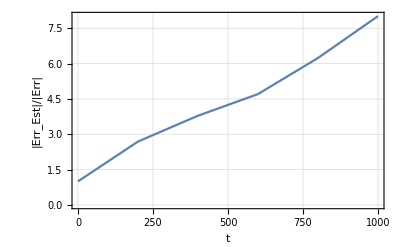

```mathematica
plot=ListPlot[{MeanQtyCdata},AxesLabel->{"t","|Err_Est|/|Err|"},Joined->True,
PlotRange->All,
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","|Err_Est|/|Err|"}]
```